# Classical Boltzmann BGK

## by Manuel Diaz, NTU, 2013.12.16

```mathematica
Quit[];
```

## Initialize Symbols & Notation

#### Change Notebook Background

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Change Notebook to it’s original colors

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

#### Load Notation package and create symbols

```mathematica
Needs["Notation`"]
```

```mathematica
Symbolize[Subscript[f, M]];
```

## 1. Equations of State

### 1.1 State equation with gas constant, R_gas

From thermodynamics, the state equation of a non reacting monoatomic gas is given by,

```mathematica
idealGas = PV->n Subscript[R, ideal] T;
idealGasMolar = PV-> m/M Subscript[R, ideal] T;
```

Where:
	n: amount of the substance in moles,
	m: average mass of molecules in the gas,
	M: molar mass of an especific gas / molecules.

The last definition can be made specific for any gas by doing: R_gas = R_ideal/M_gas. 
E.g. considere the case of air:

```mathematica
idealAir = PV-> m Subscript[R, AIR] T;
```

We with to express our state equation as independent of the system volume. Let us define,

```mathematica
massDensity = ρ -> m/V;
```

Therefore, for an specific gas, our state equation becomes,

```mathematica
idealSpecGas = P ->  ρ Subscript[R, gas] T;
```

### 1.2 State equation with Boltzman constant, k_B

```mathematica
idealGasBk = PV -> N Subscript[k, B] T;
```

Where:
	N: number of particles in the system

Again, we wish to avoid using the Volume Variable, V, of the system. Let us define the rule:

```mathematica
particleDensity=  n-> N/V;
```

Where:
	n: number particles per unit volume
	N: number of particles in the system
	V: Volumen of the system

Further more the mass density, ρ, can be defined simply as,

```mathematica
rulerho = ρ-> m n; rulePdensity = n -> ρ/m;
```

Note: the n defined here is not the same n defined section 1.1!

Therefore the equation of state becomes

```mathematica
idealGasBk2 = P -> ρ/m Subscript[k, B] T;
```

### 1.3 Relations of R_gas and k_B

What is the botlzmann relation with the gas constant, R_gas?

```mathematica
Subscript[k, B] = (P m)/(ρ T)/.idealSpecGas
```

m R_gas

let us set a subsititution rule for this last result

```mathematica
ruleRgas =R->  k/m; ruleRgas2 = k -> m R;
```

## 2. Equilibrium Distribution Function

### 2.1 Equibrium distribution function with R

The local Maxwell-Boltzmann distribution function f_mis defined as

```mathematica
Subscript[f, M] = n(1/(2 π R T))^(3/2)Exp[-1/(2R T)(v-u)^2];
```

NOTE: This is taken from JCHuang paper of 1995.

### 2.2 Equibrium distribution function with k_B

```mathematica
Subscript[f, M]/.ruleRgas//PowerExpand
```

(ⅇ^(-(m (-u+v)^2)/(2 k T)) m^(3/2) n)/(2 √2 k^(3/2) π^(3/2) T^(3/2))

e.i.:

f_M = n(m/(2 π k T))^(3/2)Exp[-m/(2k T)(v-u)^2]

NOTE: This is in agreement with Equilibrium function used in: An introduction to the Boltzmann Equation and Transport Processes in Gases, G. Kremer, Chapter 2, Equation (2.107)

When working with kinetic boltzmann equation is avangateous to define

```mathematica
ruleTheta = m/(k T)-> 1/θ; ruleTheta2 = θ -> (k T)/m; ruleTheta3 = θ-> R T;
```

```mathematica
Subscript[f, M]/.ruleRgas/.ruleTheta//PowerExpand
```

(ⅇ^(-(-u+v)^2/(2 θ)) n)/(2 √2 π^(3/2) θ^(3/2))

f_M = n/(2 π θ)^(3/2)Exp[-(v-u)^2/(2θ)]

NOTE: This is in agreement with Equilibrium function used in: Macroscopic Transport Equations for Rarefied Gas Flows, H. Struchtrup, Chapter 3, Equation (3.21)
; D

```mathematica
Clear[Subscript[f, M]];
```

## 3. The Equipartition Theorem

The equipartition theorem states that energy is shared equally amongst all energetically accesible degress of freedom of a system.

This is not a particularly surpricing result, and can be thought of as anotther way a system will generaly try to maximize its entropy (i.e. how to ‘spread out’ the energy is in the system) by distributing the available energy evenly amongts all the accesible modes of motion.

Let us consider the kinetic and potential energies associated with translational, rotational and vibrational energy.

```mathematica
Subscript[K, translational] = 1/2 mv^2
Subscript[K, rotational] = 1/2 Iω^2
Subscript[K, vibratinal] = 1/2 mv^2
Subscript[V, vibrational]= 1/2 kx^2
```

mv^2/2

Iω^2/2

mv^2/2

kx^2/2

As a consequence, equipartition contributions from vibrational degrees of freedom need only ussually be considered at very high temperatures. Conversely at room temperature many rotational and translational states are occupied, and they can be treated classically (i.e. as if their levels were not quantised) to a very good approximation.

we can use Maxwell Botlzmann distribution of molecular speeds is:

```mathematica
f[v_]:= 4π (m/(2π k T))^(3/2)v^2 Exp[-(m v^2)/(2k T)]
```

the average kinetic energy of a particle in the gas is then

```mathematica
K̄=∫_0^∞ (1/2 m v^2)f[v]ⅆv
```

ConditionalExpression[(3 k T)/2,Re[m/(k T)]>0]

The average translational kinectic enegy of a particle in a gas id therefore 3/2 kT or 1/2kT per degree of freedom.

### The Equilibrium Distribution function

define d = 1,2,3; as the dimensional parameter for

```mathematica
Subscript[f, M][v_,d_]:= n(1/(2 π θ))^(d/2)Exp[-(v-u)^2/(2θ)]; ℯ [v_,d_]:= d/2 ρ θ;
```

The equilibrium distribution in 1, 2 and 3 dimensional spaces are defined as,

```mathematica
Table[Subscript[f, M][v,d],{d,3}] //PowerExpand
```

{(ⅇ^(-(-u+v)^2/(2 θ)) n)/(√(2 π) √θ),(ⅇ^(-(-u+v)^2/(2 θ)) n)/(2 π θ),(ⅇ^(-(-u+v)^2/(2 θ)) n)/(2 √2 π^(3/2) θ^(3/2))}

and the corresponding Internal energy for particles traveling in 1,2 and 3 dimensional spaces are,

```mathematica
Table[ℯ[v,d],{d,3}]
```

{(θ ρ)/2,θ ρ,(3 θ ρ)/2}

```mathematica
Table[ℯ[v,d],{d,3}]/.ruleTheta2/.rulerho
```

{(k n T)/2,k n T,(3 k n T)/2}

```mathematica
Table[ℯ[v,d],{d,3}]/.ruleTheta2/.ruleRgas2/.rulerho
```

{1/2 m n R T,m n R T,3/2 m n R T}

## 4. Moments of the distribution function

In kinetic theory, the quantities that characterize a macroscopic state of a gas are defined in terms of the distribution function f(x,c,t).  Indeed, based on the microscopic quantities od the gas molecules like mass, m, linear momentum mc_i and energy mc^2/2, one defines the mass density ρ, momentum density ρv_iand total energy density ρu of the gas through the relationships

```mathematica
∫_(-∞)^∞ m Subscript[f, M][v,1]ⅆv
```

ConditionalExpression[m n,Re[1/θ]≥0]

Therefore we need to use traditional integration methods with assumtion to do this clean,

```mathematica
MassDensity = Integrate[m Subscript[f, M][v,1],{v,-∞,∞},Assumptions-> Re[1/θ]>0];
MomentumDensity = Integrate[m v Subscript[f, M][v,1],{v,-∞,∞},Assumptions-> Re[1/θ]>0];
TotalEnergyDensity = Integrate[m/2 v^2 Subscript[f, M][v,1],{v,-∞,∞},Assumptions-> Re[1/θ]>0];
InternalEnergyDensity = Integrate[m/2 (v-u)^2 Subscript[f, M][v,1],{v,-∞,∞},Assumptions-> Re[1/θ]>0];
```

#### Using R_gas

```mathematica
momentsR = {
MassDensity/.rulePdensity ,
MomentumDensity/.rulePdensity ,
TotalEnergyDensity/.rulePdensity/.ruleTheta3 //Expand,
InternalEnergyDensity/.rulePdensity/.ruleTheta3 }
```

{ρ,u ρ,(R T ρ)/2+(u^2 ρ)/2,(R T ρ)/2}

This last result is in agreement with moment equations shown in JC Huang paper of 1995.

#### Using K_B

```mathematica
momentskb = {
MassDensity /.rulePdensity,
MomentumDensity/.rulePdensity,
TotalEnergyDensity /.ruleTheta2 /.rulePdensity//Expand,
InternalEnergyDensity/.ruleTheta2 }
```

{ρ,u ρ,(k T ρ)/(2 m)+(u^2 ρ)/2,(k n T)/2}

#### Using θ

```mathematica
momentsth = {
MassDensity /.rulePdensity,
MomentumDensity/.rulePdensity,
TotalEnergyDensity/.rulePdensity //Expand,
InternalEnergyDensity/.rulePdensity}
```

{ρ,u ρ,(u^2 ρ)/2+(θ ρ)/2,(θ ρ)/2}

## 5. 1D Boltzmann BGK and Equilibrium Density-PDF

```mathematica
BoltzmannBGK = (d f)/(d t) + v(d f)/(d x) + (f-feq)/τ;
```

```mathematica
Feq= Simplify[Subscript[f, M][v,1]/.ruleTheta//PowerExpand,{θ>0}]
```

(ⅇ^(-(u-v)^2/(2 θ)) n)/(√(2 π) √θ)

## 6. 1D Normalization Rules

```mathematica
Clear[rulesDimensionless]
```

Set spatial dimension

```mathematica
d =1; (* spatial dimension *)
```

Set parameters

```mathematica
Subscript[n, 0]; (* reference particle density *)
Subscript[T, 0]; (* reference Temperature *)
Subscript[m, 0]; (* reference gas molecules mass *)
Subscript[C, 0] = Sqrt[2 Subscript[θ, 0]];
Subscript[t, 0] = L/Subscript[C, 0];
```

```mathematica
rulesDimensionless = {θ->Subscript[θ, 0] θ̂,t ->Subscript[t, 0] t̂ ,x->L x̂, v -> Subscript[C, 0] v̂,u -> Subscript[C, 0] û ,f ->Subscript[n, 0]/Subscript[C, 0] f̂,feq ->Subscript[n, 0]/Subscript[C, 0] OverHat[feq],τ-> Subscript[t, 0] τ̂,n-> Subscript[n, 0] n̂,m->Subscript[m, 0] m̂ };
```

### Boltzmann Equation

```mathematica
dfactor = (L /Subscript[C, 0]* Subscript[C, 0]/Subscript[n, 0]);(* but in reality I should only use the factor (L/Subscript[C, 0]) *)
```

```mathematica
dfactor*(BoltzmannBGK /.rulesDimensionless)//Expand
```

(f̂)/(t̂)+(f̂ v̂)/(x̂)+(f̂)/(τ̂)-OverHat[feq]/(τ̂)

```mathematica
dfactor=(Subscript[C, 0]/Subscript[n, 0]); (* The extra Subscript[C, 0]/Subscript[n, 0] factor is for the normalization of 'f' *)
```

```mathematica
dfactor*(Simplify[Feq/.rulesDimensionless,{R>0,θ̂>0}])//PowerExpand
```

(ⅇ^(-(û-v̂)^2/(θ̂)) n̂)/(√π √(θ̂))

In this proces θ  can take the values of θ = RT or θ = KT/m,

I’m happy with this discretization : )

### Moment Equations

```mathematica
momentsR
```

{ρ,u ρ,(R T ρ)/2+(u^2 ρ)/2,(R T ρ)/2}

```mathematica
momentskb
```

{ρ,u ρ,(k T ρ)/(2 m)+(u^2 ρ)/2,(k n T)/2}

```mathematica
momentsth
```

{ρ,u ρ,(u^2 ρ)/2+(θ ρ)/2,(θ ρ)/2}

Getting rid off dimensions:

```mathematica
ρ ==∫m feq[v]ⅆv/.rulesDimensionless //Simplify
ρu==∫m v feq[v]ⅆv/.rulesDimensionless //Simplify
ρE==∫m v^2/2 feq[v]ⅆv/.rulesDimensionless//Simplify
ρe==∫m(v-u)^2/2 feq[v]ⅆv/.rulesDimensionless //Simplify
```

Integrate::ilim: Invalid integration variable or limit(s) in √2\ v ^\ √θ_0.

ρ==(∫(OverHat[feq] n_0)/(√2 √θ_0)[√2 v̂ √θ_0]ⅆ(√2 v̂ √θ_0)) m̂ m_0

Integrate::ilim: Invalid integration variable or limit(s) in √2\ v ^\ √θ_0.

ρu==(∫√2 v̂ √θ_0 (OverHat[feq] n_0)/(√2 √θ_0)[√2 v̂ √θ_0]ⅆ(√2 v̂ √θ_0)) m̂ m_0

Integrate::ilim: Invalid integration variable or limit(s) in √2\ v ^\ √θ_0.

2 ρE==(∫2 (v̂)^2 θ_0 (OverHat[feq] n_0)/(√2 √θ_0)[√2 v̂ √θ_0]ⅆ(√2 v̂ √θ_0)) m̂ m_0

Integrate::ilim: Invalid integration variable or limit(s) in √2\ v ^\ √θ_0.

2 ρe==(∫2 (û-v̂)^2 θ_0 (OverHat[feq] n_0)/(√2 √θ_0)[√2 v̂ √θ_0]ⅆ(√2 v̂ √θ_0)) m̂ m_0

Nevermind the warnings. By observing these results, the following conclusions can be drawn:

```mathematica
conclusion = {ρ̂ ->  ρ/(Subscript[n, 0] Subscript[m, 0]), OverHat[ρu] ->  ρu/(Subscript[n, 0] Subscript[m, 0] Subscript[C, 0]), OverHat[ρE] ->  ρE/(Subscript[n, 0] Subscript[m, 0] Subscript[C, 0]^2), OverHat[ρe] ->  ρe/(Subscript[n, 0] Subscript[m, 0] Subscript[C, 0]^2)};
```

or in the form of rules

```mathematica
rulesDimensionless2 = {ρ->ρ̂ Subscript[n, 0] Subscript[m, 0],ρu->OverHat[ρu] Subscript[n, 0] Subscript[m, 0] Subscript[C, 0],ρE->OverHat[ρE] Subscript[n, 0] Subscript[m, 0] Subscript[C, 0]^2,ρe->OverHat[ρe] Subscript[n, 0] Subscript[m, 0] Subscript[C, 0]^2,θ->Subscript[θ, 0] θ̂,u -> Subscript[C, 0] û};
```

```mathematica
Solve[ρu == ρ u/.rulesDimensionless2 ,OverHat[ρu]]
Solve[ρE == (θ ρ)/2+(u^2 ρ)/2/.rulesDimensionless2 ,OverHat[ρE]]//Expand
Solve[ρe == (θ ρ)/2/.rulesDimensionless2 ,OverHat[ρe]]
```

{{OverHat[ρu]→û ρ̂}}

{{OverHat[ρE]→1/2 (û)^2 ρ̂+(θ̂ ρ̂)/4}}

{{OverHat[ρe]→(θ̂ ρ̂)/4}}

### Extra thermodynamic relations

We need to define relations between ρ, p, u with Internal Energy and Temperature

```mathematica
Clear[γ,ρ]
```

Thus pressure and internal energy are related by

```mathematica
p = (γ-1)ρe
```

(-1+γ) ρe

Therefore the internal Energy is,

```mathematica
e = P/((γ- 1)ρ);
```

Internal Enegy and temperature are related as,

```mathematica
Subscript[c, v] = R/(γ-1); e =  Subscript[c, v] T
```

(R T)/(-1+γ)

```mathematica
T = ρe/(ρ Subscript[c, v])
```

((-1+γ) ρe)/(R ρ)

## 7. 1D Example

```mathematica
ClearAll;
```

Let’s consider Sod’s shocktube problem Initial conditions,

```mathematica
{Subscript[ρ, L],Subscript[u, L],Subscript[p, L]} = {1,0.0,1};
{Subscript[ρ, R],Subscript[u, R],Subscript[p, R]} = {0.1,0.0,0.01};
```

```mathematica
ρ = {Subscript[ρ, L],Subscript[ρ, R]}; u ={Subscript[u, L],Subscript[u, R]}; p={Subscript[p, L],Subscript[p, R]};
```

therefore, for a gamma-law gas the internal energy is given by

```mathematica
γ = 1.4; m=1; n = ρ/m;
```

```mathematica
ρe = p/(γ-1)
```

{2.5,0.025}

and from normalization process we know,

```mathematica
T = (4ρe)/ρ
```

{10.,1.}

1D MB density probabilty distribution function,

```mathematica
feq = (ⅇ^(-(v-u)^2/(2 T)) n)/(√(2 π) √T)
```

{0.126157 ⅇ^(-0.05 (0.+v)^2),0.0398942 ⅇ^(-0.5 (0.+v)^2)}

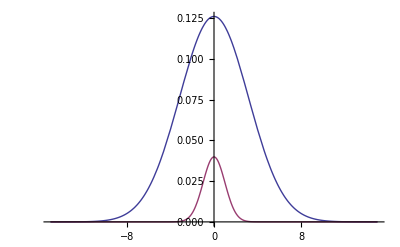

```mathematica
Plot[feq,{v,-15,15}]
```

the integration moments are,

```mathematica
ρ =∫_(-∞)^∞ m feqⅆv
```

{1.,0.1}

```mathematica
u =1/ρ∫_(-∞)^∞ m v feqⅆv
```

{0.,0.}

```mathematica
Ener =1/ρ∫_(-∞)^∞ m v^2 feqⅆv
```

{10.,1.}

```mathematica
e =1/ρ∫_(-∞)^∞ m (v-u)^2 feqⅆv
```

{10.,1.}

if we only compute Energy then,

```mathematica
e = Ener - 1/2 u^2
```

{10.,1.}

then pressure is computed as,

```mathematica
p = (γ-1) (ρ e)/4
```

{1.,0.01}

or

```mathematica
p = (γ-1)(ρ T)/4
```

{1.,0.01}